Forces on a Partially Submerged Gate

```mathematica
Manipulate[
Module[{conv1,conv2,h1,a1,a2,b,h2,A,yc,hc,Ixc,yR,hR,γ,W,FR,FT,xc,xR,scale,units,FTmax,δ,labels},
conv1=If[tab==1,1,0.3048];(*ft to m*)
conv2=If[tab==1,1,4.448];(*lbF to N*)

h1=If[tab==1,hA,hB];
a1=h1/Sin[θ];a2=8*conv1;b=4*conv1;
h2=a2*Sin[θ];

A=a1*b;
yc=a1/2;hc=yc*Sin[θ];
Ixc=1/12*b*a1^3;yR=Ixc/(yc*A)+yc;hR=yR*Sin[θ];

γ=If[tab==1,62.4,9850];(*SG: lb/ft3, kg/m3*)
W=If[tab==1,WA,WB]*1000;(*weight lbF, kN*)

FR=γ*hc*A;
FT=t/.Quiet@Solve[FR*(a1-yR)+W*b*Cos[θ]==t*a2*Sin[θ],t][[1]];

xc=x/.Quiet@Solve[0.5*a2*Sin[θ]==(h2-0)/(b+a2*Cos[θ]-b)*(x-b)+0,x][[1]];
xR=x/.Quiet@Solve[0.333*h1==(h2-0)/(b+a2*Cos[θ]-b)*(x-b)+0,x][[1]];

scale[F_]:=If[tab==1,1.75,0.53]*Rescale[F,{0,If[tab==1,(*6993*)5000,22200]}];
units=If[tab==1,Subscript[" klb","F"]," kN"];
FTmax=FT<4232*conv2;If[FTmax==False,label=False];

δ=1.2*If[tab==1,0.85,0.26];


labels=If[label,{Thin,
(*WATER HEIGHT*)
Line[{{0.25*b,0},{0.25*b,h1}}],
Text[Framed[Style[Row@{NumberForm[h1,{3,2}],If[tab==1," ft"," m"]},17],Background->RGBColor[0.6,1,0.95],FrameStyle->None,FrameMargins->Tiny],{0.25*b,0.5*h1}],

(*GATE HEIGHT*)
Line[{{0.5*b,0},{0.5*b,h2}}],
Text[Framed[Style[Row@{NumberForm[N@h2,{4,2}],If[tab==1," ft"," m"]},17],Background->White,FrameStyle->None,FrameMargins->Tiny],{0.5*b,0.75*h2}],

(*WATER LENGTH*)
Line[{{b+δ,0},{b+a1*Cos[θ]+δ,h1}}],Line[{b+#*δ,0}&/@{0.8,1.2}],Line[{b+a1*Cos[θ]+#*δ,h1}&/@{0.8,1.2}],
Text[Framed[Style[Row@{NumberForm[N@a1,{3,2}],If[tab==1," ft"," m"]},17],Background->White,FrameStyle->None,FrameMargins->Tiny],{b+0.7*a1*Cos[θ]+δ,0.7*h1}],

(*GATE LENGTH*)
Line[{{b+2*δ,0},{b+a2*Cos[θ]+2*δ,h2}}],Line[{b+2*δ+#*0.2*δ,0}&/@{-1,1}],Line[{b+a2*Cos[θ]+2*δ+#*0.2*δ,h2}&/@{-1,1}],
Text[Framed[Style[Row@{NumberForm[a2,{3,2}],If[tab==1," ft"," m"]},17],Background->White,FrameStyle->None,FrameMargins->Tiny],{b+0.7*a2*Cos[θ]+2*δ,0.7*h2}],

(*ANGLE*)
Line[{{b,0},{1.15*b,0}}],Circle[{b,0},If[tab==1,0.5,0.155],{0,θ}],
Text[Style[θ,17,Background->White],{b,0},{-3,-1}]
}];

Graphics[{Thick,Arrowheads@0.045,
(*structure*)
If[FTmax,{{FaceForm@RGBColor[0.6,1,0.95],Polygon[{{0,h1},{0,0},{b,0},{b+h1/Sin[θ]*Cos[θ],h1}}]},Line[{{0,h2},{b+a2*Cos[θ],h2}}]}],
{CapForm@None,
Thickness@0.015,Line[{{0,1.1*h2},{0,0},{b,0}}],
Thickness@0.03,If[FTmax,Line[{{b,0},{b+a2*Cos[θ],h2}}],Line[{{b,0},{2.5*b,0}}]]},
{PointSize@0.04,Point@{b,0}},

(*ground lines*)
{Thin,If[tab==1,Line[{{#,-0.5},{#+0.5,0}}]&/@Range[0,b-0.5,0.5],Line[{{#,-0.15},{#+0.15,0}}]&/@Range[0,b-0.15,0.15]]},

If[FTmax,labels],

(*TENSION*)
If[FTmax,{
{RGBColor[0,0.6,0],Arrowheads@{{-0.045,0.7},{0.045,0.3}},Arrow[{{b+a2*Cos[θ],h2},{0,h2}}],
Text[Style[Row@{NumberForm[FT/1000,{6,2}],units},18,Background->White],{(b+a2*Cos[θ])/2,h2}]},
{PointSize@0.022,Point@#,White,PointSize@0.015,Point@#}&/@{{0,h2},{b+a2*Cos[θ],h2}},

(*WEIGHT*)
{Blue,Arrow[{{xc,0.5*a2*Sin[θ]},{xc,0.5*a2*Sin[θ]-1.5*scale[W]}}],
If[W>0,Text[Style[Row@{NumberForm[N@W/1000,{6,2}],units},18,Background->White],{xc,0.5*a2*Sin[θ]-1.5*scale[W]},{0,1}]],
PointSize@0.02,Point@{xc,0.5*a2*Sin[θ]}},

(*RESULTANT*)
{Purple,Arrow[{{xR+1.2*scale[FR]*Cos[90°+θ],0.333*h1+1.2*scale[FR]*Sin[90°+θ]},{xR,0.333*h1}}],
Text[Style[Row@{NumberForm[FR/1000,{6,2}],units},18],{xR+1.2*scale[FR]*Cos[90°+θ],0.333*h1+1.2*scale[FR]*Sin[90°+θ]},{1,-1}],
PointSize@0.02,Point@{xR,0.333*h1}}
},
Text[Style["cable tension too high, cable snapped",18],If[tab==1,{4.3,6},{1.31,1.83}]]
]
},ImageSize->{600,400},PlotRange->If[tab==1,{{0,13.17},{-0.5,7.976}},{{0,4.017},{-0.15,2.431}}],PlotRangePadding->Scaled@0.02]
],
Grid[{
{Control[{{θ,60°,"angle"},30°,65°,1°,Appearance->"Labeled",ImageSize->Small}],
PaneSelector[{
1->Control[{{hA,4,"water height (ft)"},1,4,0.1,Appearance->"Labeled",ImageSize->Small}],
2->Control[{{hB,1.22,"water height (m)"},0.31,1.22,0.01,Appearance->"Labeled",ImageSize->Small}]
},Dynamic@tab],SpanFromLeft},
{PaneSelector[{
1->Control[{{WA,5,Row@{"gate weight (",Subscript["klb","F"],")"}},0,5,0.1,Appearance->"Labeled"}],
2->Control[{{WB,22.2,"gate weight (kN)"},0,22.2,0.1,Appearance->"Labeled"}]
},Dynamic@tab],SpanFromLeft,
Control[{{tab,2,"units"},{1->" US customary ",2->" SI "},Setter}],Spacer@5,
Control[{{label,False,"show labels"},{True,False}}]}
},Alignment->Left]
]
```

A gate, which is hinged at the bottom, is partially submerged under water, and a cable holds the gate closed. Set the angle of the gate, the weight of the gate, and the water height with sliders. Change the units from klb_F (force) and feet (US customary units) to kN and meters (SI units) with buttons. Check the "show labels" box to display distances. The demonstration displays the cable tension needed to hold up the gate. When the tension is too high (4.23 klb_F or 18.82 kN), the cable breaks.





Determine the cable tension necessary to hold a gate that is b feet wide at the base, a_2 feet long diagonally, and a_1 feet of diagonal length is submerged under water (see Figure 1).

The magnitude of the resultant force is found by summing the differential forces ⅆF=γ h ⅆA over the entire surface:

F_R=∫_A γ h ⅆA=∫_A γ y sin θ ⅆA,

where F_R is the resultant force (N), γ is the specific weight of the fluid (kg/m^3), h=y sin θ is the vertical distance from the fluid surface to the centroid center (m), y is the y-coordinate of the height along the diagonal (see Figure 2 for a coordinate system), θ is the angle (degrees), and A=a_1 b is area (m^2).

For constant γ and θ, the resultant force becomes:

F_R=γ sin θ ∫_A y ⅆA.

The previous integral ∫_A y ⅆA is the first moment of the area with respect to the x-axis, so:

F_R=∫_A y ⅆA=y_c A,

where y_c=a_1/2 is the y-coordinate of the centroid of area measured from the x-axis that passes through 0.

The resultant force can be written as:

F_R=γ A y_c sin θ=γ h_c A,

where h_c is the vertical distance from the fluid surface to the centroid of area.

The y-coordinate y_R of the resultant force is determined by summing the moments around the x-axis. Thus, the moment of the resultant force must equal the moment of the distributed pressure forces, or:

F_R y_R=∫_A γ y^2 sin θ ⅆA.

Therefore, since F_R=γ A y_c sin θ:

y_R=(∫_A y^2 ⅆA)/(y_c A).

The integral in the numerator is the second moment of the area (moment of inertia) I_x, with respect to an axis formed by the intersection of the plane containing the surface and the free surface (x-axis):

y_R=I_x/(y_c A).

Since I_x=I_(x c)+A y_c^2, where I_(x c) is the second moment of the area with respect to an axis passing through its centroid and parallel to the x-axis (m^4):

y_R=(I_(x c))/(y_c A)+y_c,

where I_(x c)=1/12 b a_1^3.

A moment balance determines the tension in the cable that is holding up the gate:

∑M=0=F_R (a_1-y_R)+W b cos θ-T a_2 sin θ.

Rearranging to solve for tension:

T=(F_R (a_1-y_R)+W b cos θ)/(a_2 sin θ),

where T is tension (N), and W is the weight of the gate (N).

Figure 1

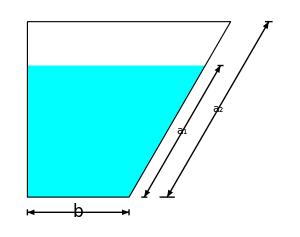

Figure 2

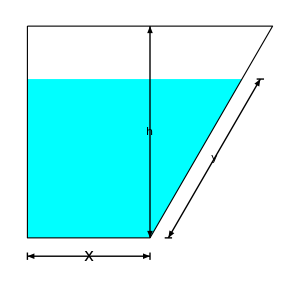

Reference

[1] W.W. Huebsch, B.R. Munson, T.H. Okiishi, and D.F. Young, Fundamentals of Fluid Mechanics, 6th ed., New Jersey: John Wiley & Sons, 2009, pp. 57-60.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

chemical engineering

mechanical engineering

fluids

fluids gate

gate

submerged area

submerged gate

Contributed by: Rachael L. Baumann

Additional contributions by: John L. Falconer

(University of Colorado Boulder, Department of Chemical and Biological Engineering)